# Problem 1

```mathematica
zeros = ZetaZero/@ Range[1,500]//N//(#-1/2)/I&//Re;
```

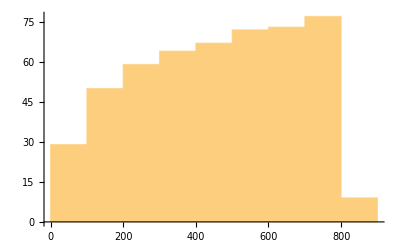

```mathematica
zeros//Histogram
```

# Problem 2

See Wolfram Demonstrations

# Problem 3

```mathematica
content =Import["http://perimeterinstitute.ca/conferences/mathematica-summer-school-2015","XMLObject"]
```

```mathematica
pos=Position[content,a_String/;StringMatchQ[a,___~~"Andrew"~~___],∞][[1]]
```

{2,3,2,3,4,3,8,3,4,3,2,3,2,3,4,3,2,3,7,3,1,3,1,3,1,3,2,3,2,3,1,3,1,3,1,3,2,3,21,3,1,3,1}

```mathematica
xmlNames=pos[[;;-6]]
```

{2,3,2,3,4,3,8,3,4,3,2,3,2,3,4,3,2,3,7,3,1,3,1,3,1,3,2,3,2,3,1,3,1,3,1,3,2,3}

```mathematica
content[[Sequence@@xmlNames]]
```

```mathematica
Cases[content[[Sequence@@xmlNames]],XMLElement["strong",{},{name_}]:>name,∞]
```

{Nima Afkhami-Jeddi,Mikhail Alfimov, ,Natacha Altamirano,Alexander Avdoshkin,Srivatsan Balakrishnan,Alessio Belenchia, ,Davide Bianchini, ,Alex Blatov, ,Thomas Bohdanowicz,Daniel Brod,Chris Brust,Isak Buhl-Mortensen,Marcello Davide Caio,Giancarlo Camilo,Pawel Caputa,Horacio Casini,Christopher Chamberland,Aidan Chatwin-Davies,Hanzhe Chen,Frank Coronado,Andrew Day,Anton De la Fuente,Kenan Diab,Arpit Dua,,Damian Galante,Dongwook Ghim,Roy Gomel,Lucia Gomez Cordova,James Gordon,Nikolay Gromov,Lucas Hackl,Jason Harris,Michal Heller,Andrew Hickling,Edward Hughes,Nicholas Hunter-Jones,Nafiz Ishtiaque,,Aron Jansen,Laurens Kabir,Joonho Kim,Martyna Kostacinska,Aitor Lewkowycz,Bruno Lima de Souza,Gabriel Magill,Juan Maldacena,Ipsita Mandal,Lauren McGough,Marco Meineri,David Meltzer,Mark Mezei,Deyan Mihaylov,Seyed Faroogh Moosavian,Robert Myers,Yuki Nakaguchi,Jun Nian,Takuya Nishmura,,Alexander Patrushev,Arttu Pönni,Petter Säeterskog,Marco Sanchioni,Jaspreet Sandhu,Barak Shoshany,,John Stout,Sotaro Sugishita,Sivaramakrishnan Swaminathan,Wilke van der Schee,Guifre Vidal,Pedro Viera,Manus Visser,Kento Watanabe,Erik Widen,Jason Wien,Dom Williamson,Elie Wolfe,Yasaman Yazdi,Ellis Yuan,Huangjun Zhu,Michael Zlotnikov,Claire Zukowski}

```mathematica
RandomChoice[%,5]
```

{Alexander Avdoshkin,Aron Jansen,Pedro Viera,Robert Myers,Jason Harris}

# Problem 4

```mathematica
RandomizeCapitalization[s_String]:=StringJoin@@(RandomChoice[{ToUpperCase@#,ToLowerCase@#}]&)/@Characters@s
```

```mathematica
RandomizeCapitalization@"Fabulous"
```

FaBULOus

```mathematica
NotebookPut[NotebookGet[EvaluationNotebook[]]/."Problem 1":>"Problem One"];
```

```mathematica
hackerize[nb_]:=Block[{content,symbols,identifiers,replacements},
content = NotebookGet @ nb;
symbols=Union@Cases[content,a_String?LetterQ,∞];
identifiers=Complement[symbols,Names@"System`*"];
replacements=(#->RandomizeCapitalization@#&)/@identifiers;
NotebookPut[content/.replacements]]
```

# Problem 5

```mathematica
lindep[x_]:=Block[{len,y},
y=Round[10^50 x];
len=Length[y];
Most[LatticeReduce[mat=(IdentityMatrix[len]~Join~{-y}ᵀ)~Join~{0*Range[len+1]}]⟦1⟧]]
```

```mathematica
num=Zeta[3]+5 Zeta[5]+11Zeta[7]//N[#,20]&
```

17.478537730077595012

```mathematica
mat
```

(1 | 0 | 0 | 0 | -1747853773007759501229433864214438518664871470578338
0 | 1 | 0 | 0 | -120205690315959428539973816151144999076498629234050
0 | 0 | 1 | 0 | -103692775514336992633136548645703416805708091950191
0 | 0 | 0 | 1 | -100834927738192282683979754984979675959986356056524
0 | 0 | 0 | 0 | 0)

```mathematica
LatticeReduce[mat]
```

(-1 | 1 | 5 | 11 | -17535028431
308169462998 | 10977702607935 | 2747275536648 | -21253450091807 | -4583324974
3583570760234 | -12468187764477 | -27994054838902 | -18466114416084 | -3331506944
-4742777144317 | 89798869142731 | -64765317278660 | 41761733473538 | 3425776744)

```mathematica
mat[[1]]-mat[[2]]-5mat[[3]]-11 mat[[4]]
```

{1,-1,-5,-11,0}

```mathematica
lindep[{num,Zeta[3],Zeta[5],Zeta[7]}]
```

{-1,1,5,11}